=== Test 1: Simple autocatalytic ===

Testing RN1: {a→a+b,b→a+b,a→0,b→0}

Species from extSpe: {a,b}

Rxn 1: a→a+b -> reactants={a}, T={a,b}, internal=True

Rxn 2: b→a+b -> reactants={b}, T={a,b}, internal=True

Rxn 3: a→0 -> reactants={a}, T={a,b}, internal=True

Rxn 4: b→0 -> reactants={b}, T={a,b}, internal=True

Cores found: 0

All results: {<|T→{a,b},isCore→If[Indeterminate>1/1000000000000,Association[isCore→True,t→tsol$7615,flux→AssociationThread[{1,2,3,4}→vsol$7615],gammaT→gammaT$7615,netProd→gammaT$7615.vsol$7615],Association[isCore→False,reason→max t <= 0,t→tsol$7615]][isCore],intReacIdx→{1,2,3,4},details→If[Indeterminate>1/1000000000000,Association[isCore→True,t→tsol$7615,flux→AssociationThread[{1,2,3,4}→vsol$7615],gammaT→gammaT$7615,netProd→gammaT$7615.vsol$7615],Association[isCore→False,reason→max t <= 0,t→tsol$7615]]|>}

=== Test 2: Three-strain chain ===

Minimal siphons: {{i1},{i2},{i3}}

Rxn 1: 0→s -> reactants={}, T={i1}, internal=True

Rxn 2: s→0 -> reactants={s}, T={i1}, internal=False

Rxn 3: i1+s→2 i1 -> reactants={i1,s}, T={i1}, internal=False

Rxn 4: i1→0 -> reactants={i1}, T={i1}, internal=True

Rxn 5: i1+i2→2 i2 -> reactants={i1,i2}, T={i1}, internal=False

Rxn 6: i2→0 -> reactants={i2}, T={i1}, internal=False

Rxn 7: i2+i3→2 i3 -> reactants={i2,i3}, T={i1}, internal=False

Rxn 8: i3→0 -> reactants={i3}, T={i1}, internal=False

LinearProgramming::argb: LinearProgramming called with 2 arguments; between 3 and 5 arguments are expected.

Rxn 1: 0→s -> reactants={}, T={i2}, internal=True

Rxn 2: s→0 -> reactants={s}, T={i2}, internal=False

Rxn 3: i1+s→2 i1 -> reactants={i1,s}, T={i2}, internal=False

Rxn 4: i1→0 -> reactants={i1}, T={i2}, internal=False

Rxn 5: i1+i2→2 i2 -> reactants={i1,i2}, T={i2}, internal=False

Rxn 6: i2→0 -> reactants={i2}, T={i2}, internal=True

Rxn 7: i2+i3→2 i3 -> reactants={i2,i3}, T={i2}, internal=False

Rxn 8: i3→0 -> reactants={i3}, T={i2}, internal=False

LinearProgramming::argb: LinearProgramming called with 2 arguments; between 3 and 5 arguments are expected.

General::stop: Further output of LinearProgramming::argb will be suppressed during this calculation.

Rxn 1: 0→s -> reactants={}, T={i3}, internal=True

Rxn 2: s→0 -> reactants={s}, T={i3}, internal=False

Rxn 3: i1+s→2 i1 -> reactants={i1,s}, T={i3}, internal=False

Rxn 4: i1→0 -> reactants={i1}, T={i3}, internal=False

Rxn 5: i1+i2→2 i2 -> reactants={i1,i2}, T={i3}, internal=False

Rxn 6: i2→0 -> reactants={i2}, T={i3}, internal=False

Rxn 7: i2+i3→2 i3 -> reactants={i2,i3}, T={i3}, internal=False

Rxn 8: i3→0 -> reactants={i3}, T={i3}, internal=True

Cores found: 0

Load CRNT

reactions and transitions: (0→S | La
S→0 | mu0 s
I1+S→2 I1 | be1 i1 s
I1→0 | i1 mu1
I1+I2→2 I2 | i1 i2 ro12
I2→0 | i2 mu2
I2+I3→2 I3 | i2 i3 ro23
I3→0 | i3 mu3)

Minimal siphons: {T_1={i1},T_2={i2},T_3={i3}}

IGMS edges: {1→2,2→3}

IGMS is acyclic (no cycles found)

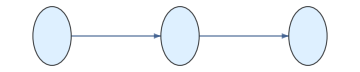

siphons are{{i1},{i2},{i3}} edges are{1→2,2→3}  DFE is{s→La/mu0,i1→0,i2→0,i3→0} repr. functions  {(be1 s)/mu1}

K=((be1 s)/mu1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)F=(be1 s | 0 | 0
0 | 0 | 0
0 | 0 | 0)V=(mu1 | 0 | 0
0 | mu2 | 0
0 | 0 | mu3)

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;
(*Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];Format[mu3]:=Subscript[μ,3];Format[mu0]:=Subscript[μ,0];
Format[R1]:=Subscript[R,1];Format[R2]:=Subscript[R,2];Format[R3]:=Subscript[R,3];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[ga1]:=Subscript[γ,1];Format[ro12]:=Subscript[ρ,12];Format[ro23]:=Subscript[ρ,23];Format[ga2]:=Subscript[γ,2];Format[s0]:=Subscript[s,0];
Format[th]:=θ;
Format[La]:=Λ;
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i3]:=Subscript[i,3];
Format[i12]:=Subscript[i,12];*)

cLog={be1->0,be2->0,ga1->0,ga2->0,b->r*s*(1-s/s0),mu0->0};
cbg={be1->0,be2->0,ga1->0,ga2->0};
cbe={be1->0,be2->0};cb=b->s0 mu0;cga={ga1->0,ga2->0};
cet={et1->s13 mu1 mu3 (R1-R3)/((s0-s13)mu0 s0),
et2->s23 mu2 mu3 (R2-R3)/((s0-s23)mu0 s0)};
cmu={mu2 ->mu,mu3->mu,mu1 ->mu,mu0->mu};
c3={i12->0};c2={i2->0};c1={i1->0};cb=b->r*s*(1-s/s0);
RN={0->"S","S"->0,"S"+"I1"->2*"I1","I1"->0,"I1"+"I2"->2*"I2","I2"->0,"I2"+"I3"->2*"I3","I3"->0};
rts={La,mu0*s,be1*s*i1,mu1*i1,ro12*i1*i2,mu2*i2,ro23*i2*i3,mu3*i3};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RN,rts];
{edg,cyc,graph}=IGMS[RN, mSi];
Print["siphons are",mSi," edges are",edg,"  DFE is",E0," repr. functions  ",R0A];F=ng[[2]];V=ng[[3]];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];
```

```mathematica
(*---------------------------------------------------------------------findCores[RN,opts]:find autocatalytic cores (minimal autocatalytic subnetworks)-Uses extMat[RN] to obtain {"species",...,"gamma"} as in your EpidCRN (species=RND[[1]],gamma=RND[[4]])-Uses parsing of RN LHS/RHS to identify reactant/product sets (robust to Symbols or Strings)-CandidateSets->list of candidate species-sets to test (recommended:minimal siphons)-If CandidateSets->Automatic,enumerates all nonempty subsets up to MaxSize (default 6)-Returns Association with "Cores" list and full diagnostics---------------------------------------------------------------------*)ClearAll[parseComplexTerms,getReactProdSets,findInternalReactionsByParsing,isAutocatalyticBlockLP,findCores];

(*parse a complex expression (0 or sum of terms) into list of species names (strings)*)
parseComplexTerms[0]:={};
parseComplexTerms[c_]:=Module[{terms=If[Head[c]===Plus,List@@c,{c}],atoms},atoms=DeleteDuplicates[Cases[terms,(m_?NumericQ)*s_Symbol:>s|(m_?NumericQ)*s_String:>s|s_Symbol:>s|s_String:>s,{0,Infinity}]];
ToString/@atoms];

(*Given RN,return lists reactantSets and productSets (each element is list of species names as strings)*)
getReactProdSets[RN_List]:=Module[{n=Length[RN],lhs,rhs},Table[lhs=RN[[j,1]];rhs=RN[[j,2]];
{parseComplexTerms[lhs],parseComplexTerms[rhs]},{j,n}]];

(*Find internal reactions for a given candidate T (strings or symbols ok) by parsing reactants*)
findInternalReactionsByParsing[RN_List,T_List]:=Module[{Tstr=ToString/@T,rp,reactantsList,out},rp=getReactProdSets[RN];
reactantsList=rp[[All,1]];(*list of reactant species lists (strings)*)out=Flatten@Position[reactantsList,r_/;(r=!={}&&SubsetQ[r,Tstr])&];
out];

(*LP-based test:given gamma (full stoichiometric matrix),speciesIndices in T,internal reaction indices,determine if exists v>=0 with gamma_T v>=t*1_m and return max t and example v.We implement as LinearProgramming minimizing-t.*)
isAutocatalyticBlockLP[gamma_,speciesIdx_List,intReacIdx_List,vmin_:10^-9]:=Module[{gammaT,m,n,A,b,c,sol,tsol,vsol},If[intReacIdx==={}||speciesIdx==={},Return[<|"isCore"->False,"reason"->"empty block"|>]];
gammaT=If[Length[speciesIdx]==1,{gamma[[speciesIdx[[1]],intReacIdx]]},gamma[[speciesIdx,intReacIdx]]];
m=Length[speciesIdx];n=Length[intReacIdx];
(*Form constraints:gammaT.v-t>=0 (m inequalities) v_j>=vmin (n inequalities) t>=0*)(*A.x>=b with x={v_1..v_n,t} length n+1*)A=Join[Map[Join[#,{-1}]&,gammaT],(*m rows*)Table[Join[Table[If[i==j,1,0],{i,n}],{0}],{j,n}],(*v_j>=vmin*){Join[Table[0,{n}],{1}]}  (*t>=0*)];
b=Join[ConstantArray[0,m],ConstantArray[vmin,n],{0}];
c=Join[Table[0,{n}],{-1}];(*minimize-t->maximize t*)(*Solve LP;enforce nonnegativity bounds for safety*)sol=Quiet@LinearProgramming[Rationalize[c],Rationalize[A],Rationalize[b],Table[{0,Infinity},{n+1}]];
If[sol===$Failed||sol==={},Return[<|"isCore"->False,"reason"->"LP failed or infeasible"|>]];
tsol=N[sol[[n+1]]];
vsol=N[Take[sol,n]];
If[tsol>10^-12,<|"isCore"->True,"t"->tsol,"v"->AssociationThread[intReacIdx->vsol],"gammaT"->gammaT|>,<|"isCore"->False,"reason"->"max t <= 0","t"->tsol,"gammaT"->gammaT|>]];

(*main function:findCores*)
Options[findCores]={"CandidateSets"->Automatic,"MaxSize"->6,"RequireColumnReactProdInT"->True};
findCores[RN_List,opts:OptionsPattern[]]:=Module[{RND,species,gamma,nSpec,nReac,rp,reactantSets,productSets,candidateSets,cand,maxSize,requireColCond,results,tested=0,isCoreRes,speciesIdxMap},(*extMat extraction:adapt if your extMat returns different ordering*)RND=extMat[RN];(*expects RND[[1]] species,RND[[4]] gamma*)species=RND[[1]];
gamma=RND[[4]];
nSpec=Length[species];nReac=Length[RN];
speciesIdxMap=AssociationThread[ToString/@species->Range[nSpec]];
(*get parsed reactant/product sets*)rp=getReactProdSets[RN];
reactantSets=rp[[All,1]];
productSets=rp[[All,2]];
(*determine candidate sets*)candidateSets=OptionValue["CandidateSets"];
maxSize=OptionValue["MaxSize"];
requireColCond=OptionValue["RequireColumnReactProdInT"];
If[candidateSets===Automatic,candidateSets=Rest@Subsets[ToString/@species,{1,Min[maxSize,nSpec]}]  (*nonempty subsets up to maxSize*),(*canonicalize candidateSets to strings*)candidateSets=ToString/@(#)&/@candidateSets;];
results=Reap[Do[tested++;
Module[{T=candidateSets[[k]],intReacIdx,speciesIdx,colOkQ,colIndices,lpres},(*internal reactions via parsing of reactants*)intReacIdx=findInternalReactionsByParsing[RN,T];
If[intReacIdx==={},Sow[<|"T"->T,"isCore"->False,"reason"->"no internal reactions"|>];Continue[]];
(*column condition:for each internal reaction j,require at least one reactant in T and at least one product in T*)colOkQ=True;
colIndices=Select[intReacIdx,(Module[{rset=reactantSets[[#]],pset=productSets[[#]],ok},ok=True;
If[requireColCond,If[!(Intersection[rset,T]=!={}&&Intersection[pset,T]=!={}),ok=False];];
ok])&];
If[colIndices==={},Sow[<|"T"->T,"isCore"->False,"reason"->"columns do not satisfy reactant/product-in-T condition","intReacIdx"->intReacIdx|>];Continue[]];
(*species indices*)speciesIdx=speciesIdxMap/@T;
(*LP test*)lpres=isAutocatalyticBlockLP[gamma,speciesIdx,colIndices];
If[lpres["isCore"],Sow[<|"T"->T,"isCore"->True,"intReacIdx"->colIndices,"t"->lpres["t"],"v"->lpres["v"],"gammaT"->lpres["gammaT"]|>],Sow[<|"T"->T,"isCore"->False,"reason"->lpres["reason"],"t"->lpres["t"],"gammaT"->lpres["gammaT"]|>]];],{k,Length[candidateSets]}]][[2,1]];
(*Filter only true cores and reduce to minimal ones (no proper subset that is also core)*)Module[{cores=Select[results,#["isCore"]===True&],minimal},minimal=Select[cores,Function[c,Not[MemberQ[DeleteCases[cores,c],d_/;SubsetQ[ToString/@d["T"],ToString/@c["T"]]&&d["T"]=!=c["T"]]]]];
<|"Species"->species,"GammaDimensions"->Dimensions[gamma],"Tested"->tested,"AllResults"->results,"Cores"->minimal|>]];

(*--------------------Example usage--------------------*)
(*Use your RN;here the simple autocatalytic example*)
RNexample={A->A+B,B->A+B,A->0,B->0};
(*If you already have minimal siphons,pass them as CandidateSets->{{"A","B"}}*)
res=findCores[RNexample,"CandidateSets"->{{"A","B"}}];
res//InputForm
```

RuleDelayed::rhs: Pattern m_ appears on the right-hand side of rule s_Symbol m_?NumericQ:>s|m_?NumericQ s_String:>s|s_Symbol:>s|s_String:>s.

RuleDelayed::rhs: Pattern s_String appears on the right-hand side of rule s_Symbol m_?NumericQ:>s|m_?NumericQ s_String:>s|s_Symbol:>s|s_String:>s.

RuleDelayed::rhs: Pattern s_Symbol appears on the right-hand side of rule s_Symbol m_?NumericQ:>s|m_?NumericQ s_String:>s|s_Symbol:>s|s_String:>s.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

<|"Species" -> {"a", "b"}, "GammaDimensions" -> {2, 4}, "Tested" -> 1, 
 "AllResults" -> {<|"T" -> {"A", "B"}, "isCore" -> False, 
    "reason" -> "no internal reactions"|>}, "Cores" -> {}|>

```mathematica
?EpidCRN`*
```